## MKP pre 1D rovnicu vedenia tepla NESTACIONÁRNE

### Integrácia cez kvadratúry

```mathematica
GaussNodesWeights[n_]:=Module[{x,P,dP,xi,wi},
P=LegendreP[n,x]; (*Legendreho polynóm n-teho stupňa*)
dP=D[P,x];
xi=x/. NSolve[P==0&&-1<x<1,x]; (*nájde všetky korene Pn na (-1,1), gaussove uzly*)
xi=N[xi];
wi=N[2/((1-xi^2) (dP/. x->xi)^2)]; (*váhy*)
Transpose[{xi,wi}] (*zoznam párov xi-uzly, wi-váhy*)
];

{xi,wi}=Transpose[GaussNodesWeights[3]]; (*3 bodová*)

(*Numerická Gaussova kvadratúra na interval[a,b]*)
GaussQuad[f_,x_,a_,b_]:=
Module[{c=(a+b)/2, (*stred intervalu*)
h=(b-a)/2}, (*1/2 intervalu*)
N@(h*Total[wi*(f/. x->(c+h*xi))]) (*za x doasdím všetky body c + hξi​*)
];
```

Parametre ulohy

```mathematica
Clear[f,u0, c1, a];
xL=0;xP=1;(*Hranice vypoctovej oblasti*)
c1[x_]:=1;(*pri časovej derivácií, súčiniteľ*);
a[x_]:=1+x;(*materialova charakteristika*)
Clear[f];
f[x_]:=-18 x^2;(*zdroj PS*)
α1=1;β1=0;g1=1;(*Paramtre lavej OP*)
α2=0;β2=1;g2=0;(*Paramtre pravej OP*)
u0[x_]:=1+2 x-x^2;(*pociatocna podmienka, máme čas!*)
```

Presne riesenie

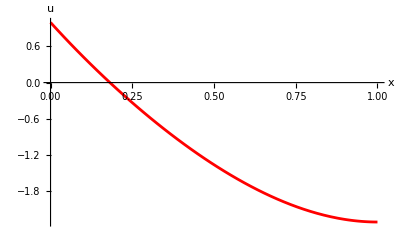

```mathematica
Rovnica=-D[a[x]u'[x],x]==f[x];
riesenie=DSolve[{
Rovnica,
α1 u[xL]+β1 (-a[xL]u'[xL])==g1,
α2 u[xP]+β2 (a[xP]u'[xP])==g2
},u[x],x];
uA[x_]=u[x]/.riesenie[[1]];
plotA=Plot[uA[x], {x,xL,xP},AxesLabel->{Style[x,Large],Style[u,Large]},PlotStyle->Red]
```

MKP, diskretizacia oblasti, Časová, priestorová

```mathematica
(*---Priestorová sieť---*)
s=1;(*stupeň elementu:1=lineárny (2 prvky na elemente),2=kvadratický...*)
NN=4;(*počet elementov, počet rovníc*)
n=s*NN+1;(*počet globálnych uzlov, pre lin = NN +1*)
H=(xP-xL)/NN;(*dĺžka jedného elementu*)
h = H/s;(*vzdialenosť susedných globálnych uzlov*)


(*---Časová diskretizácia---*)
(*
α=0 - explicitna schema, 
α=1 - implicitna schema, 
α=0.5 - Crank-Nicolson schema, 
α=2/3 - Galerkinova schema,
*)

α=1;          (*implicitná Eulerova schéma, stabilná*)
k = 1;
τ=k*H^2; (*časový krok*)
Tend=3;             (*koniec času*)
NT=Ceiling[Tend/τ]; (*počet časových krokov*)
```

MKP, zostrojenie aproximacnych funkcii (Lagrangeov tvar)

```mathematica
(*UZLY A INDEXY----------------------------------------------------*)
(*VŠETKY globálne uzly*)
uzly=Table[xL+j*h,{j,0,NN*s}];    (*dĺžka=NN*s+1*)

  (*pre daný element e vráti s+1 uzlov*)
uzlyNaElemente[e_]:=uzly[[(e-1)*s+1;;(e-1)*s+s+1]];

(*vracia číselné indexy*)
globIdx[e_]:=Range[(e-1)*s+1,(e-1)*s+s+1];

(*aproximačné funkcie*)
psiLagrange[x_,loc_,i_]:=
 (*loc - zoznam lokálnyhc uzlov na e*)
(*i-index požadovanej bázy (1,2,...,Length[loc]*)
Product[
If[j==i,
1, (*kronekerova delta*)
(x-loc[[j]])/(loc[[i]]-loc[[j]])],
{j,1,Length[loc]}
];

(*pole aproximačných funkcií na elemente, symbolicky*)
(*výpočet naprieč elementami*)
(*dvojitý zoznam [[e]] - zoznam bázy na elemente, [[e,i]] - konkrétna funkcia*)
psiVsetky=
Table[
With[
{loc=uzlyNaElemente[e]},
Table[psiLagrange[x,loc,i],{i,1,Length[loc]
}
]
],
{e,1,NN}];

(*derivácie aproximačných funkcií*)
dpsiVsetky=Table[D[psiVsetky[[e,i]],x],{e,1,NN},{i,1,Length[psiVsetky[[e]]]}];



Show[Table[With[{loc=uzlyNaElemente[e],funs=psiVsetky[[e]]},Plot[Evaluate[funs],{x,First[loc],Last[loc]},PlotLegends->None]],{e,1,NN}],PlotRange->All,PlotLabel->"Lagrangeove bázy po elementoch"];


Print["e = 1, 1.AF psiVsetky[[1,1]] = ",psiVsetky[[1,1]]];
Print["e = 1, 2.AF psiVsetky[[1,2]] = ",psiVsetky[[1,2]]];
```

e = 1, 1.AF psiVsetky[[1,1]] = -4 (-1/4+x)

e = 1, 2.AF psiVsetky[[1,2]] = 4 x

MKP, zostrojenie lokalnych matic a pravych stran, M, K, F

```mathematica
(*LOKÁLNE MATICE*)
(*zintegrujem cez celý element*)
(*zoznamy zoznamov*)

elementK=Table[
Module[
{loc,m,xA,xB,psi,dpsi,Ke},
loc=uzlyNaElemente[e];
m=Length[loc];
xA=First[loc];
xB=Last[loc];
psi=psiVsetky[[e]];
dpsi=dpsiVsetky[[e]];
Ke=N@Table[GaussQuad[a[x]*dpsi[[i]]*dpsi[[j]],x,xA,xB],{i,m},{j,m}];
Ke
],
{e,1,NN}
];

(*hmotnostná funkcia, nestacionárne*)
elementM=Table[
Module[
{loc,m,xA,xB,psi,Me},
loc=uzlyNaElemente[e];
m=Length[loc];
xA=First[loc];
xB=Last[loc];
psi=psiVsetky[[e]];
Me=N@Table[GaussQuad[c1[x]*psi[[i]]*psi[[j]],x,xA,xB],{i,m},{j,m}];
Me
],{e,1,NN}];


(*elementové F bez času, nezávisí od času*)
elementF=Table[
Module[
{loc,m,xA,xB,psi},
loc=uzlyNaElemente[e];
m=Length[loc];
xA=First[loc];
xB=Last[loc];
psi=psiVsetky[[e]];
N@Table[GaussQuad[f[x]*psi[[i]],x,xA,xB],{i,m}]],
{e,1,NN}
];

(*čo element, to zoznam zoznamov*)
(*každý element -> jedna lokálna K,f,M*)
(*dlžka zoznamu-> počet elementov NN, dlĺžka "podzoznamov-> stupeň elementu"*)
elementK  
elementM 
elementF
```

{{{4.5,-4.5},{-4.5,4.5}},{{5.5,-5.5},{-5.5,5.5}},{{6.5,-6.5},{-6.5,6.5}},{{7.5,-7.5},{-7.5,7.5}}}

{{{0.0833333,0.0416667},{0.0416667,0.0833333}},{{0.0833333,0.0416667},{0.0416667,0.0833333}},{{0.0833333,0.0416667},{0.0416667,0.0833333}},{{0.0833333,0.0416667},{0.0416667,0.0833333}}}

{{-0.0234375,-0.0703125},{-0.257812,-0.398437},{-0.773437,-1.00781},{-1.57031,-1.89844}}

MKP, zostrojenie globalnych matic a pravych stran

```mathematica
(*Montáž*)
(*v zdieľaných uzloch sa príspevky sčítajú, viem podľa globId*)
(*Najprv zistím,ktoré globálne uzly element má,potom jeho lokálnu rovnicu „rozsypem“ do globálnej rovnice na tieto pozície.*)
GlobK=ConstantArray[0.,{n,n}];
Do[
Module[
{Ke,g},
Ke=elementK[[e]];
g=globIdx[e]; (*globálne indexy uzlov na elemente e*)

(*pridávanie Ke do GlobK na pozície (g_i,g_j)*)
Do[
GlobK[[g[[i]],g[[j]]]]+=Ke[[i,j]],
{i,Length[g]},{j,Length[g]}]
;],
{e,1,NN}
];

K0=GlobK; 

GlobM=ConstantArray[0.,{n,n}];
Do[
Module[
{Me,g},Me=elementM[[e]];
g=globIdx[e];
Do[GlobM[[g[[i]],g[[j]]]]+=Me[[i,j]],{i,Length[g]},{j,Length[g]}]
;],
{e,1,NN}
];

GlobF=Module[{F=ConstantArray[0.,n]},
Do[
With[{g=globIdx[e]},
(*vektorovo:priamo pripočítam lokálny Fe do správnych globálnych pozícií*)
F[[g]]+=elementF[[e]]
;
],
{e,1,NN}
];
F
];
```

Okrajové podmienky

```mathematica
(*počiatočné podmienky*)
(*U0–vektor hodnôt u0(x)v uzloch -> to je aproximácia u(x,0)*)
U0=N@Table[u0[uzly[[i]]],{i,n}];

(*Newton/Neumann príspevok do tuhostnej matice:K+α1/β1,α2/β2*)
GlobKbc=GlobK;
If[
β1!=0,GlobKbc[[1,1]]+=α1/β1
];
If[
β2!=0,GlobKbc[[n,n]]+=α2/β2
];

(*príspevok g/β do pravej strany *)
GlobFbc=GlobF;
If[
β1!=0,GlobFbc[[1]]+=g1/β1
];  
If[
β2!=0,GlobFbc[[n]]+=g2/β2
];

(*K,M konštantné časovo nezávislé, OP pred časovým cyklom*)
(*matica H bez Dirichleta*)
Hbase = GlobM+α GlobKbc*τ; 


(*zapracovanie dirichleta do matice H0*)
H0=Hbase;

If[
α1!=0,
H0[[1,All]]=0;
H0[[1,1]]=1;
];

If[
α2!=0,
H0[[n,All]]=0;
H0[[n,n]]=0;
H0[[n,n]]=1;
];




(*Zapracovanie dirichleta, G-OP(okrajove p.) po zapracovani OP*)
AplikujOP[G_,t_]:=Module[
{GOP=G,val},
(*ľavý Dirichlet,ak α1≠0*)
If[α1!=0,
val=g1/α1;
GOP[[1]]=val;
];
(*pravý Dirichlet,ak α2≠0*)
If[α2!=0,
val=g2/α2;
GOP[[n]]=val;
];
GOP
];



(*Pole riešení*)
(*NT počet časových krokov, n-počet glob.uzlov*)
(*riadok = časový krok, stĺpec = priestorový uzol*)
Un=ConstantArray[0.,{NT+1,n}]; (*riešenie v čase tk*)
Un[[1]]=U0; (*prvý časový krok je počiatočná podmienka*)

(*len na ukladanie pravých strán*)
Gstore=ConstantArray[0.,{NT+1,n}]; (*bez Dirichleta*)
GOPstore=ConstantArray[0.,{NT+1,n}]; (*s Dirichletom*)


(*časový cyklus*)
Do[
tn=(k-1)*τ; (*čas t_n*)
tn1=k*τ;          (*čas t_{n+1}*)
Gn1=(GlobM-(1-α)*τ* GlobKbc).Un[[k]]+τ *GlobFbc;  
Gstore[[k]]=Gn1;

(*zohľadním Dirichleta v čase t_{n+1}*)
GOP=AplikujOP[Gn1,tn1];
GOPstore[[k]]=GOP;

(*Riešim H0*U{n+1}=GOP*)
Un[[k+1]]=LinearSolve[H0,GOP];,
{k,1,NT}
];

H0//MatrixForm;
GOP//MatrixForm;

Do[Print["n = ",n];
Print["H = ",MatrixForm[N[H0],6]];
Print["G = ",MatrixForm[N[GOPstore[[n+1]]],6]];,{n,0,1}]
```

n = 0

H = (1. | 0. | 0. | 0. | 0.
-0.239583 | 0.791667 | -0.302083 | 0. | 0.
0. | -0.302083 | 0.916667 | -0.364583 | 0.
0. | 0. | -0.364583 | 1.04167 | -0.427083
0. | 0. | 0. | -0.427083 | 0.552083)

G = (1.
0.333659
0.359049
0.318034
0.128743)

n = 1

H = (1. | 0. | 0. | 0. | 0.
-0.239583 | 0.791667 | -0.302083 | 0. | 0.
0. | -0.302083 | 0.916667 | -0.364583 | 0.
0. | 0. | -0.364583 | 1.04167 | -0.427083
0. | 0. | 0. | -0.427083 | 0.552083)

G = (1.
0.27748
0.244161
0.150427
0.0331943)

MKP, riesenie rovnic, konstrukcia priblizneho riesenia, zobrazenie presneho aj priblizneho riesenia

```mathematica
Clear[uMKPAt];

Clear[uMKPAt];

uMKPAt[U_][x_]:=Piecewise[
Table[
With[
{
loc=uzlyNaElemente[e],
idx=globIdx[e]
},
{
U[[idx]].psiVsetky[[e]],(*hodnota na elemente*)
loc[[1]]<=x<=loc[[-1]]          (*interval elementu [xe​,xe+1​]*)
}],
{e,1,NN}]];
```

```mathematica
frames=Table[
Module[
{tval=(k-1)*τ,(*čas t_{k-1}*)
uFE
},
uFE=uMKPAt[Un[[k]]];(*MKP riešenie v čase tval*)
Show[
{
Plot[u0[x],{x,xL,xP},PlotLegends->{"u0(x)"},PlotRange->All],Plot[uA[x],{x,xL,xP},PlotLegends->{"uA(x)"},PlotRange->All],Plot[uFE[x],{x,xL,xP},PlotLegends->{"U(x,t_n)"},PlotRange->All]
},
PlotLabel->Row[{"t = ",NumberForm[tval,{4,3}]}]]],{k,1,NT+1}];

ListAnimate[frames, DefaultDuration->60]
```

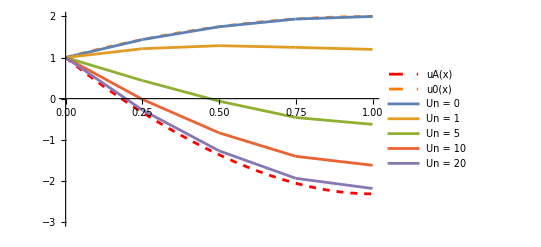

```mathematica
(*indexy v zozname Un pre n=0,1,5,10,20*)
(*idx={1,2,6,11,21};*)
idx={1,2, 6, 11, 21};

UMKP=Plot[
Evaluate@Table[uMKPAt[Un[[k]]][x],{k,idx}],
{x,xL,xP},
PlotRange->All,
AxesLabel->{"x","u"},
PlotLegends->("Un = "<>ToString[#-1]&/@idx)];

uAA=Plot[uA[x],{x,xL,xP},PlotLegends->{"uA(x)"},PlotStyle->{Thick,Dashed,Red}];
u00=Plot[u0[x],{x,xL,xP},PlotLegends->{"u0(x)"},PlotStyle->{Thick,Dashed,Orange}];

Show[uAA,u00,UMKP,PlotRange->{-3,2}]
```